```mathematica
getCov = Module[{meanx,meany,covXX,covYY,covXY,dim},
meanx = Mean[  #ᵀ[[1]]  ];
meany = Mean[  #ᵀ[[2]]  ];
dim=Dimensions[#][[1]];

covXX = 4Total[(#[[1]]-meanx)^2&/@#]/(dim-1);
covYY = 4Total[(#[[2]]-meany)^2&/@#]/(dim-1);
covXY = 4Total[(#[[1]]-meanx)(#[[2]]-meany)&/@#]/(dim-1);

{{{covXX,covXY},{covXY,covYY}},meanx,meany}
]&;
getEllipsoid=Module[{},
Graphics[{
EdgeForm[{Thick,ColorData[3,"ColorList"][[#2]]}],
FaceForm[None],
Ellipsoid[#1[[2;;3]],#1[[1]]]
}]
]&;
```

## Ellipsoid plot, all twirls

```mathematica
couplingIdx=15;
covs12=getCov[#]&/@(dats12[[couplingIdx]]);
covs23=getCov[#]&/@(dats23[[couplingIdx]]);
theoryByTwirls={Re[#],Im[#]}&/@theory;

ellipses12=Table[
getEllipsoid[covs12[[idx]],idx]
,{idx,1,10}];
ellipses23=Table[
getEllipsoid[covs23[[idx]],idx]
,{idx,1,10}];

markersTheory=Table[
coords = theoryByTwirls[[idx]];
Graphics[{
EdgeForm[{Black}],
FaceForm[ColorData[3,"ColorList"][[idx]]],
Rectangle[{coords[[1]],coords[[2]]}-{0.05,0.05},{coords[[1]],coords[[2]]}+{0.05,0.05}]
}]
,{idx,1,10}];
Clear[coords]

dummyplot=ListPlot[{0,0}
,PlotMarkers->Style[•,White]
,AspectRatio->1
,PlotRange->{{-1.8,2.8},{-2.6,2.6}}
,Frame->True
,FrameLabel->{{Style["Imaginary part",25],None},{Style["Real part",25],Style[StringJoin[
"Jones Poly, σ_23 braid word\nQubits: ",
ToString[couplingTable[[couplingIdx,1]]],
" and ",
ToString[couplingTable[[couplingIdx,2]]]
],30]}}
];
```

### Fine tuning label coordinates, to make them easier to see

```mathematica
baseX=0.0;
baseY=0.18;
theoryCoords=theoryByTwirls+{
{baseX,baseY},
{baseX,baseY},
{baseX,baseY-0.35},
{baseX,baseY},
{baseX,baseY},
{baseX-0.1,baseY},
{baseX,baseY},
{baseX,baseY},
{baseX,baseY},
{baseX,baseY-0.35}
};
labelsTheory=Table[
Graphics[
Style[
Text[idx-1,theoryCoords[[idx]]],
18
]
]
,{idx,1,10}];
```

```mathematica
baseX=0.1;
baseY=0.1;
ellipses12Coords=(#[[2;;3]]&/@covs12)+{
{baseX-0.3,baseY+0.05},
{baseX,baseY+0.1},
{baseX+0.2,baseY-0.1},
{baseX-0.25,baseY},
{baseX-0.28,baseY+0.1},
{baseX-0.27,baseY-0.2},
{baseX-0.1,baseY+0.05},
{baseX-0.1,baseY+0.07},
{baseX+0.15,baseY-0.1},
{baseX,baseY+0.1}
};
ellipses23Coords=(#[[2;;3]]&/@covs23)+{
{baseX-0.3,baseY+0.05},
{baseX,baseY+0.1},
{baseX+0.2,baseY-0.1},
{baseX-0.25,baseY},
{baseX-0.28,baseY+0.1},
{baseX-0.27,baseY-0.2},
{baseX-0.1,baseY+0.05},
{baseX-0.1,baseY+0.07},
{baseX+0.15,baseY-0.1},
{baseX,baseY+0.1}
};

labelsEllipse12=Table[
Graphics[
Style[
Text[Superscript[Subscript["σ","12"],idx-1],ellipses12Coords[[idx]]],
15
]
]
,{idx,1,10}];
labelsEllipse23=Table[
Graphics[
Style[
Text[Superscript[Subscript["σ","23"],idx-1],ellipses23Coords[[idx]]],
15
]
]
,{idx,1,10}];
```

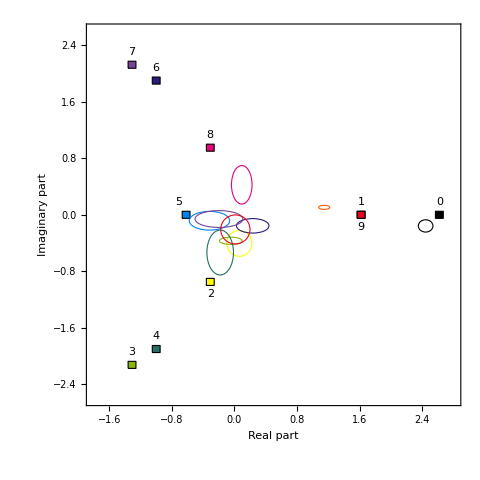

```mathematica
Show[
dummyplot,
markersTheory,
labelsTheory,
ellipses23(*,
labelsEllipse23*)
]
```